Kyungwon Chun, kwchun@biobrain.kr
Oct. 21, 2019

The other lecture notes can be doanloaded at https://github.com/ruddyscent/gsa-2019-fall.

```mathematica
<<SymbolicComputing`

boilerplateTemplate=StringTemplate["This notebook depends on Mathematica `ver` and MathSymbolica `scVer`. Also, the contents reflect the last execution on `date`."];
Print[boilerplateTemplate[<|"scVer"->$SCVersion,"ver"->$Version, "date"->DateString[]|>]]
```

This notebook depends on Mathematica 12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019) and MathSymbolica 5.1.2 (July 22, 2019). Also, the contents reflect the last execution on Mon 21 Oct 2019 10:09:57.

## Problem of the week 3/5

## Problem

-Graphics-

## Solution

### 1)

-Graphics-

Naive approach using basic Wolfram language commands:

```mathematica
Cos[A]^3+Cos[B]^3+Cos[C]^3≥3Cos[A] Cos[B] Cos[C]
SCMAF[%,RA,{All,C==π-A-B},
{#&&0<A&&0<B&&A+B<π}&,All,
Reduce,{All,{A,B},Reals}]
```

Cos[A]^3+Cos[B]^3+Cos[C]^3≥3 Cos[A] Cos[B] Cos[C]

{Cos[A]^3+Cos[B]^3-Cos[A+B]^3≥-3 Cos[A] Cos[B] Cos[A+B]&&0<A&&0<B&&A+B<π}

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

SCMAF::stopped: Stopped due to error.

Reduce[{Cos[A]^3+Cos[B]^3-Cos[A+B]^3≥-3 Cos[A] Cos[B] Cos[A+B]&&0<A&&0<B&&A+B<π},{A,B},ℝ]

Our first approach fails. This time, tackle the problem with a graphical tool, Plot3D:

```mathematica
SCARA[{Cos[A]^3+Cos[B]^3+Cos[C]^3,3Cos[A]Cos[B]Cos[C]},C==π-A-B]
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},AxesLabel->{A,B},PlotLegends->{LHS,RHS}},Take->{2}]
```

{Cos[A]^3+Cos[B]^3+Cos[C]^3,3 Cos[A] Cos[B] Cos[C]}=={Cos[A]^3+Cos[B]^3-Cos[A+B]^3,-3 Cos[A] Cos[B] Cos[A+B]}

-Graphics3D-

Though RHS is bigger than LHS in some region, it seems that the the region does not satisfy the angle restriction of a triangle.

```mathematica
SCARA[{Cos[A]^3+Cos[B]^3+Cos[C]^3,3Cos[A]Cos[B]Cos[C]},C==π-A-B]
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},RegionFunction->Function[{A,B},π>A+B],AxesLabel->{A,B},PlotLegends->{LHS,RHS}},Take->{2}]
```

{Cos[A]^3+Cos[B]^3+Cos[C]^3,3 Cos[A] Cos[B] Cos[C]}=={Cos[A]^3+Cos[B]^3-Cos[A+B]^3,-3 Cos[A] Cos[B] Cos[A+B]}

-Graphics3D-

It seems that the two surface is too close at a point. May be it cross over in a small region that we can not noticible in this scale. Let’s check it.

```mathematica
F==Cos[A]^3+Cos[B]^3+Cos[C]^3-3Cos[A]Cos[B]Cos[C]
SCMAF[%,RA,{At[2],C==π-A-B}]
```

F==Cos[A]^3+Cos[B]^3-3 Cos[A] Cos[B] Cos[C]+Cos[C]^3

F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3

The function, F should be greather than or equal to 0 to satisfy the given inequality.

```mathematica
F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},RegionFunction->Function[{A,B},π>A+B],AxesLabel->{A,B,F}},Take->{2}]
```

F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3

-Graphics3D-

We can observe that a minimum point is close to 0. Let’s find the location of the minimum.

```mathematica
{(∂F)/(∂A)==0,(∂F)/(∂B)==0}
SCMAF[%,RA,{All,F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3},Post->SCDerivExpand,
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π,0<B<π}},
DeleteCases,{All,{False,_}},,,,
DeleteCases,{All,{_,False}},Post->N,IgnoreError->True]
```

{(∂F)/(∂A)==0,(∂F)/(∂B)==0}

Root::deg: -1+2 (SymbolicComputing`Private`Slot$$1)^3 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{{A==1.0472,B==1.0472},{A==1.5708,B==1.5708},{A==2.28021,B==2.28021}}

The thrid solution does not satisfy the triangle restriction.

```mathematica
{(∂F)/(∂A)==0,(∂F)/(∂B)==0}
SCMAF[%,RA,{All,F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3},Post->SCDerivExpand,
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π,0<B<π}},
DeleteCases,{All,{False,_}},,,,
DeleteCases,{All,{_,False}},Take->{1,2},IgnoreError->True]
```

{(∂F)/(∂A)==0,(∂F)/(∂B)==0}

Root::deg: -1+2 (SymbolicComputing`Private`Slot$$1)^3 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{{A==π/3,B==π/3},{A==π/2,B==π/2}}

The minimum seems to be located inside in A+B<π/2, so the location of minum should be the first solution

```mathematica
F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3
SCMAF[%,RA,{At[2],{A==π/3,B==π/3}}]
```

F==Cos[A]^3+Cos[B]^3+3 Cos[A] Cos[B] Cos[A+B]-Cos[A+B]^3

F==0

The value is not less than 0. Therefore, the given inequality is proved.

### 2)

-Graphics-

Naive approach using basic Wolfram language commands:

```mathematica
3(Sin[A]^2+Sin[B]^2+Sin[C]^2)-2(Cos[A]^3+Cos[B]^3+Cos[C]^3)≤6
SCMAF[%,RA,{All,C==π-A-B},
{#&&0<A&&0<B&&A+B<π}&,All,
Reduce,{All,{A,B},Reals}]
```

-2 (Cos[A]^3+Cos[B]^3+Cos[C]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[C]^2)≤6

{-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)≤6&&0<A&&0<B&&A+B<π}

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

SCMAF::stopped: Stopped due to error.

Reduce[{-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)≤6&&0<A&&0<B&&A+B<π},{A,B},ℝ]

Our first approach fails. This time, tackle the problem with a graphical tool, Plot3D:

```mathematica
SCARA[{3(Sin[A]^2+Sin[B]^2+Sin[C]^2)-2(Cos[A]^3+Cos[B]^3+Cos[C]^3),6},C==π-A-B]
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},AxesLabel->{A,B},PlotLegends->{LHS,RHS}},Take->{2}]
```

{-2 (Cos[A]^3+Cos[B]^3+Cos[C]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[C]^2),6}=={-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2),6}

-Graphics3D-

Though LHS is bigger than RHS in some region, it seems that the the region does not satisfy the angle restriction of a triangle.

```mathematica
SCARA[{3(Sin[A]^2+Sin[B]^2+Sin[C]^2)-2(Cos[A]^3+Cos[B]^3+Cos[C]^3),6},C==π-A-B]
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},RegionFunction->Function[{A,B},π>A+B],AxesLabel->{A,B},PlotLegends->{LHS,RHS}},Take->{2}]
```

{-2 (Cos[A]^3+Cos[B]^3+Cos[C]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[C]^2),6}=={-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2),6}

-Graphics3D-

It seems that the two surface is too close at a point. May be it cross over in a small region that we can not noticible in this scale. Let’s check it.

```mathematica
F==3(Sin[A]^2+Sin[B]^2+Sin[C]^2)-2(Cos[A]^3+Cos[B]^3+Cos[C]^3)-6
SCMAF[%,RA,{At[2],C==π-A-B}]
```

F==-6-2 (Cos[A]^3+Cos[B]^3+Cos[C]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[C]^2)

F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)

The function, F should be less than or equal to 0 to satisfy the given inequality.

```mathematica
F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)
SCMAF[%,Plot3D,{At[2],{A,0,π},{B,0,π},RegionFunction->Function[{A,B},π>A+B],AxesLabel->{A,B,F}},Take->{2}]
```

F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)

-Graphics3D-

We can observe that a maximum point is close to 0. Let’s find the location of the maximum.

```mathematica
{(∂F)/(∂A)==0,(∂F)/(∂B)==0}
SCMAF[%,RA,{All,F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)},Post->SCDerivExpand,
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π,0<B<π}},
DeleteCases,{All,{False,_}},,,,
DeleteCases,{All,{_,False}},Post->N,IgnoreError->True]
```

{(∂F)/(∂A)==0,(∂F)/(∂B)==0}

Root::deg: -1+2 (SymbolicComputing`Private`Slot$$1)^3 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{{A==1.0472,B==1.0472},{A==1.5708,B==1.5708},{A==2.28021,B==2.28021}}

The thrid solution does not satisfy the triangle restriction.

```mathematica
{(∂F)/(∂A)==0,(∂F)/(∂B)==0}
SCMAF[%,RA,{All,F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)},Post->SCDerivExpand,
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π,0<B<π}},
DeleteCases,{All,{False,_}},,,,
DeleteCases,{All,{_,False}},Take->{1,2},IgnoreError->True]
```

{(∂F)/(∂A)==0,(∂F)/(∂B)==0}

Root::deg: -1+2 (SymbolicComputing`Private`Slot$$1)^3 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{{A==π/3,B==π/3},{A==π/2,B==π/2}}

The minimum seems to be located inside in A+B<π/2, so the location of minum should be the first solution

```mathematica
F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)
SCMAF[%,RA,{At[2],{A==π/3,B==π/3}}]
```

F==-6-2 (Cos[A]^3+Cos[B]^3-Cos[A+B]^3)+3 (Sin[A]^2+Sin[B]^2+Sin[A+B]^2)

F==0

The value is not greater than 0, so the given inequality is proved.

### 3)

-Graphics-

Naive approach using basic Wolfram language commands:

```mathematica
Cos[A]^n+Cos[B]^n+Cos[C]^n≥3/2^n
SCMAF[%,RA,{All,C==π-A-B},
{#&&0<A&&0<B&&A+B<π&&n≥2&&n∈Integers}&,All,
Reduce,{All,{A,B},Reals}]
```

Cos[A]^n+Cos[B]^n+Cos[C]^n≥3 2^-n

{Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n≥3 2^-n&&0<A&&0<B&&A+B<π&&n≥2&&n∈ℤ}

$Aborted

Our first approach fails.

Define a function, F_n:

```mathematica
Subscript[F, n]==Cos[A]^n+Cos[B]^n+Cos[C]^n-3/2^n
SCMAF[%,RA,{At[2],C==π-A-B}]
```

F_n==-3 2^-n+Cos[A]^n+Cos[B]^n+Cos[C]^n

F_n==-3 2^-n+Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n

Plot F_nfor n=1,2,3,4,5

```mathematica
Range[5]
Table[-3 2^-n+Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n,{n,%}]
SCMAF[%,Plot3D,{All,{A,0,π},{B,0,π},RegionFunction->Function[{A,B},A>0&&B>0&&A+B<π],AxesLabel->{A,B,F},PlotLegends->StringTemplate["n=``"]/@%%}]
```

{1,2,3,4,5}

{-3/2+Cos[A]+Cos[B]-Cos[A+B],-3/4+Cos[A]^2+Cos[B]^2+Cos[A+B]^2,-3/8+Cos[A]^3+Cos[B]^3-Cos[A+B]^3,-3/16+Cos[A]^4+Cos[B]^4+Cos[A+B]^4,-3/32+Cos[A]^5+Cos[B]^5-Cos[A+B]^5}

-Graphics3D-

Wow, the problem is wrong. For n=1, the inequality should be reversed. However, for n≥2, the given inequality seems to be satisfied. Let’s find the location of minimum using the partial derivation:

```mathematica
SCARA[{(∂Subscript[F, n])/(∂A),(∂Subscript[F, n])/(∂B)},Subscript[F, n]==-3 2^-n+Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n]
SCMAF[%,SCDerivExpand,{At[2]},PostAll->Thread]
```

{(∂F_n)/(∂A),(∂F_n)/(∂B)}=={(∂(-3 2^-n+Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n))/(∂A),(∂(-3 2^-n+Cos[A]^n+Cos[B]^n+(-Cos[A+B])^n))/(∂B)}

{(∂F_n)/(∂A)==-n Cos[A]^(-1+n) Sin[A]+n Sin[A+B] (-Cos[A+B])^(-1+n),(∂F_n)/(∂B)==-n Cos[B]^(-1+n) Sin[B]+n Sin[A+B] (-Cos[A+B])^(-1+n)}

```mathematica
{(∂Subscript[F, n])/(∂A)==-n Cos[A]^(-1+n) Sin[A]+n Sin[A+B] (-Cos[A+B])^(-1+n),(∂Subscript[F, n])/(∂B)==-n Cos[B]^(-1+n) Sin[B]+n Sin[A+B] (-Cos[A+B])^(-1+n)}/.n->2
SCMAF[%,RA,{All,{(∂Subscript[F, 2])/(∂A)==0,(∂Subscript[F, 2])/(∂B)==0}},
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π/2,0<B<π/2}},
DeleteCases,{All,{False,_}},,,
DeleteCases,{All,{_,False}}]
```

{(∂F_2)/(∂A)==-2 Cos[A] Sin[A]-2 Cos[A+B] Sin[A+B],(∂F_2)/(∂B)==-2 Cos[B] Sin[B]-2 Cos[A+B] Sin[A+B]}

{{A==π/3,B==π/3}}

```mathematica
{(∂Subscript[F, n])/(∂A)==-n Cos[A]^(-1+n) Sin[A]+n Sin[A+B] (-Cos[A+B])^(-1+n),(∂Subscript[F, n])/(∂B)==-n Cos[B]^(-1+n) Sin[B]+n Sin[A+B] (-Cos[A+B])^(-1+n)}/.n->3
SCMAF[%,RA,{All,{(∂Subscript[F, _])/(∂A_)==0}},
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π/2,0<B<π/2}},
DeleteCases,{All,{False,_}},,,
DeleteCases,{All,{_,False}},IgnoreError->True]
```

{(∂F_3)/(∂A)==-3 Cos[A]^2 Sin[A]+3 Cos[A+B]^2 Sin[A+B],(∂F_3)/(∂B)==-3 Cos[B]^2 Sin[B]+3 Cos[A+B]^2 Sin[A+B]}

Root::pfun: z$1$1 is not a pure function in 1 variables.

{{A==π/3,B==π/3},{A==ArcTan[(Root0.402Root[{-2-3 #1+2 #1^2+4 #1^3&,-1+#1^2+#2^2&},{1,2}]0.402116287844908)/(Root0.916Root[-2-3 #1+2 #1^2+4 #1^3&,1]0.9155886036041685)],B==ArcTan[(Root0.402Root[{-2-3 #1+2 #1^2+4 #1^3&,-3 #1^3+#1^4+5 #1^5+3 #1^6+22 #1^7-4 #1^8-56 #1^9+32 #1^11+#1^2 #2+#1^3 #2-3 #1^4 #2-#1^5 #2+2 #1^6 #2-#1^2 #2^2+#1^4 #2^2&,-1+#1^2+#3^2&,#1^2 #3+7 #1^3 #3+4 #1^4 #3+12 #1^5 #3+8 #1^6 #3-64 #1^7 #3-32 #1^8 #3+64 #1^9 #3-#2 #3-#1^2 #2 #3-12 #1^3 #2 #3+16 #1^5 #2 #3+#2^3 #3-#1 #4+#1^3 #4&},{1,2,2,1}]0.402116287844908)/(Root0.916Root[{-2-3 #1+2 #1^2+4 #1^3&,-3 #1^3+#1^4+5 #1^5+3 #1^6+22 #1^7-4 #1^8-56 #1^9+32 #1^11+#1^2 #2+#1^3 #2-3 #1^4 #2-#1^5 #2+2 #1^6 #2-#1^2 #2^2+#1^4 #2^2&},{1,2}]0.9155886036041685)]}}

```mathematica
{(∂Subscript[F, n])/(∂A)==-n Cos[A]^(-1+n) Sin[A]+n Sin[A+B] (-Cos[A+B])^(-1+n),(∂Subscript[F, n])/(∂B)==-n Cos[B]^(-1+n) Sin[B]+n Sin[A+B] (-Cos[A+B])^(-1+n)}/.n->4
SCMAF[%,RA,{All,{(∂Subscript[F, _])/(∂A_)==0}},
SCSolve,{All,{A,B}},
Refine,{All,{C[1]==0,C[2]==0,0<A<π/2,0<B<π/2}},
DeleteCases,{All,{False,_}},,,
DeleteCases,{All,{_,False}},IgnoreError->True]
```

{(∂F_4)/(∂A)==-4 Cos[A]^3 Sin[A]-4 Cos[A+B]^3 Sin[A+B],(∂F_4)/(∂B)==-4 Cos[B]^3 Sin[B]-4 Cos[A+B]^3 Sin[A+B]}

Root::deg: 2-5 (SymbolicComputing`Private`Slot$$1)^2+4 (SymbolicComputing`Private`Slot$$1)^4 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{{A==π/3,B==π/3}}

## The best fit of the given data

-Graphics-
p.21 of [2].

We will investigate the annual mean data of global CO_2 concentration from the Global Greenhouse Gas Reference Network.

```mathematica
co2Level=Import["ftp://aftp.cmdl.noaa.gov/products/trends/co2/co2_annmean_mlo.txt","Table"];
co2Level=DeleteCases[co2Level,{"#",___}];
co2Level=Take[#,2]&/@co2Level
```

{{1959,315.97},{1960,316.91},{1961,317.64},{1962,318.45},{1963,318.99},{1964,319.62},{1965,320.04},{1966,321.38},{1967,322.16},{1968,323.04},{1969,324.62},{1970,325.68},{1971,326.32},{1972,327.45},{1973,329.68},{1974,330.18},{1975,331.11},{1976,332.04},{1977,333.83},{1978,335.4},{1979,336.84},{1980,338.75},{1981,340.11},{1982,341.45},{1983,343.05},{1984,344.65},{1985,346.12},{1986,347.42},{1987,349.19},{1988,351.57},{1989,353.12},{1990,354.39},{1991,355.61},{1992,356.45},{1993,357.1},{1994,358.83},{1995,360.82},{1996,362.61},{1997,363.73},{1998,366.7},{1999,368.38},{2000,369.55},{2001,371.14},{2002,373.28},{2003,375.8},{2004,377.52},{2005,379.8},{2006,381.9},{2007,383.79},{2008,385.6},{2009,387.43},{2010,389.9},{2011,391.65},{2012,393.85},{2013,396.52},{2014,398.65},{2015,400.83},{2016,404.24},{2017,406.55},{2018,408.52}}

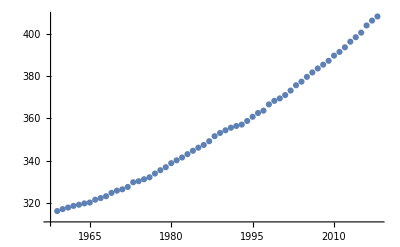

```mathematica
ListPlot[co2Level]
```

Piecewise gradient analysis shows that the increase rate of  CO_2 concentration becomes steeper.

```mathematica
FindFormula[co2Level,x,"TargetFunctions"->{Plus,Times}]
```

Piecewise[{{-1485.31+0.919214 x, 1959.≤x<1973.22}, {-2598.62+1.48339 x, 1973.22≤x<1983.3}, {-2615.52+1.492 x, 1983.3≤x<1987.76}, {-3163.82+1.76725 x, 1987.76≤x<2010.25}, {-4621.+2.4925 x, 2010.25≤x<2018.}, {0, True}}]

The CO_2 concentration can be represented using a polynomial to estimate CO_2 concentration in the future.

```mathematica
poly1=Fit[co2Level, {1,x}, x]
```

-2758.94+1.56567 x

```mathematica
poly2=Fit[co2Level, {1,x,x^2}, x]
```

47068.2-48.5534 x+0.0126022 x^2

```mathematica
poly3=Fit[co2Level, {1,x,x^2,x^3}, x]
```

-126610.+213.494 x-0.119185 x^2+0.0000220916 x^3

```mathematica
poly10=Fit[co2Level,Table[x^n,{n,0,10}],x]
```

-5.81385×10^10+9.37784×10^7 x-28660.8 x^2-17.7707 x^3+0.00303828 x^4+5.00619×10^-6 x^5+7.40944×10^-10 x^6-1.14258×10^-12 x^7-4.58072×10^-16 x^8+3.8401×10^-19 x^9-6.0486×10^-23 x^10

```mathematica
poly13=Fit[co2Level,Table[x^n,{n,0,13}],x]
```

-1.42667×10^10+1.6065×10^7 x+242.083 x^2-2.9019 x^3-0.00117855 x^4+8.69356×10^-8 x^5+3.25701×10^-10 x^6+1.62099×10^-13 x^7+9.32304×10^-18 x^8-3.83532×10^-20 x^9-2.33751×10^-23 x^10+6.81408×10^-28 x^11+8.32259×10^-30 x^12-1.88398×10^-33 x^13

Which polynomial does represent the data most accurately? Let’s compare the root mean square (RMS) of each polynomial:

```mathematica
rms1=Sqrt@Mean[((poly1/.x->#⟦1⟧)-#⟦2⟧)^2&/@co2Level]
```

3.44808

```mathematica
rms2=Sqrt@Mean[((poly2/.x->#⟦1⟧)-#⟦2⟧)^2&/@co2Level]
```

0.685836

```mathematica
rms3=Sqrt@Mean[((poly3/.x->#⟦1⟧)-#⟦2⟧)^2&/@co2Level]
```

0.679905

It seems that the error(RMS) generally decreases as the order of polynomial increases.

```mathematica
poly=ParallelTable[Fit[co2Level,Table[x^n,{n,0,nn}],x],{nn,70}];
```

```mathematica
rms=ParallelTable[Sqrt@Mean[((poly⟦nn⟧/.x->#⟦1⟧)-#⟦2⟧)^2&/@co2Level],{nn,70}]
```

{3.44808,0.685836,0.679905,0.505041,0.491397,0.491259,0.491119,0.467512,0.467707,0.4679,0.468095,0.468286,0.468479,0.468673,0.468864,0.469056,0.469247,0.469438,0.437194,0.437052,0.436885,0.436719,0.436573,0.436424,0.436265,0.436121,0.435969,0.435816,0.435669,0.43552,0.435374,0.435229,0.435084,0.434942,0.4348,0.43466,0.425426,0.425522,0.425621,0.425713,0.425817,0.425918,0.426004,0.426103,0.426197,0.426295,0.426387,0.426478,0.426569,0.42666,0.42675,0.42684,0.426928,0.427016,0.427102,0.427187,0.427273,0.427357,0.427439,0.427521,0.427602,0.42768,0.427759,0.427836,0.399843,0.399566,0.399271,0.399016,0.398752,0.398474}

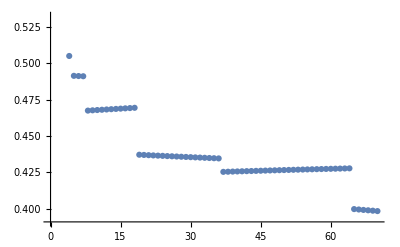

```mathematica
ListPlot@rms
```

The plot also shows that the higher-order polynomial represent the data more accurately:

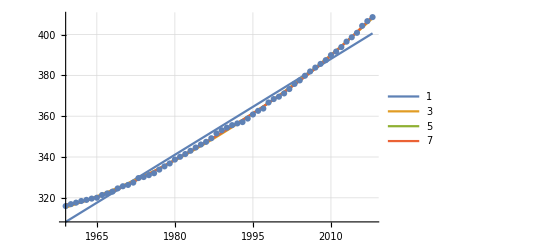

```mathematica
Show[Plot[{poly⟦1⟧,poly⟦3⟧,poly⟦5⟧,poly⟦7⟧},{x,1959,2018},PlotLegends->{1,3,5,7},GridLines->Automatic],ListPlot[co2Level]]
```

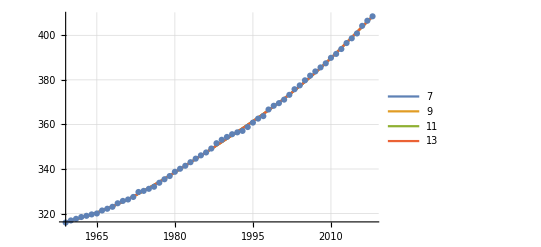

```mathematica
Show[Plot[Evaluate@Table[poly⟦n⟧,{n,9,15,2}],{x,1959,2018},PlotLegends->Range[7,15,2],GridLines->Automatic],ListPlot[co2Level]]
```

Does higher-order polynomial estimate the CO_2 concentration in the future more accurately?

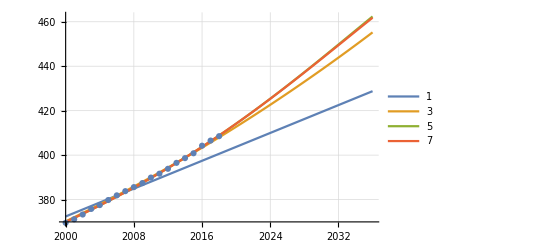

```mathematica
Show[Plot[{poly⟦1⟧,poly⟦3⟧,poly⟦5⟧,poly⟦7⟧},{x,2000,2036},PlotLegends->{1,3,5,7},GridLines->Automatic],ListPlot[co2Level]]
```

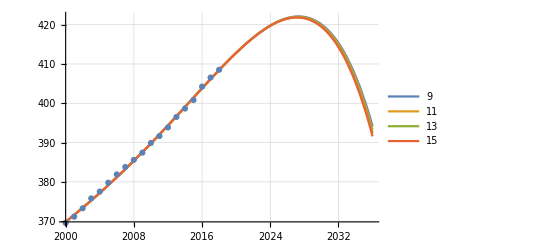

```mathematica
Show[Plot[{poly⟦9⟧,poly⟦11⟧,poly⟦13⟧,poly⟦15⟧},{x,2000,2036},PlotLegends->{9,11,13,15},GridLines->Automatic],ListPlot[co2Level]]
```

In this analysis, the 7th order polynomial is the best fit of the data.